```mathematica
ket0= {1, 0};
ket1 = {0,1};
(* Defines H = - \sigma_x / 2 and subsequent Z(t) evolution *)
H= -PauliMatrix[1]/2;
u =  MatrixExp[-ⅈ H t];
udg = MatrixExp[ⅈ H t];
zt= udg.PauliMatrix[3].u;
sx = PauliMatrix[1];
sz = PauliMatrix[3];
```

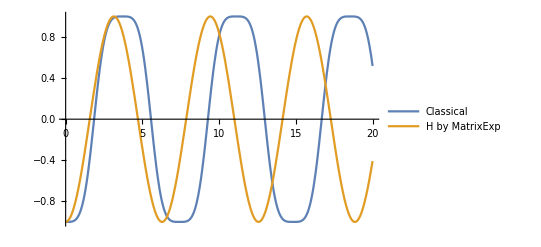

```mathematica
(* Compute <1| Z(t)|1> in both cases and compare to classical solution*)
ztExpVal = ket1.zt.ket1;
tf = 20;
dt = 0.1;
csol = NDSolveValue[{x''[t]+ Cos[x[t]]==0, x[0]==π,x'[0]==0}, x, {t, 0, tf}];
Plot[{Cos[csol[t]],ztExpVal} , {t, 0, tf}, PlotLegends->{"Classical", "H by MatrixExp"}]
```

```mathematica
phi[t_] = Table[Subscript[ϕ, i][t],{i, 1, 2}];
initState = ket1;
phiSol = NDSolveValue[{phi'[t]+ⅈ H.phi[t]==ConstantArray[0, 2], phi[0]==initState}, phi[t], {t, 0, tf}];
```

```mathematica
rho[t_]:=Table[Subscript[ρ, i,j][t], {i, 1, 2}, {j, 1, 2}];
rhoInit = KroneckerProduct[ket1, ket1];
rhoSchroSol = NDSolveValue[{Flatten[rho'[t]+ⅈ(H.rho[t]-rho[t].H)]==ConstantArray[0,4], rho[0]==rhoInit},rho[t], {t, 0, tf}];
```

```mathematica
γ = 0.05;
rhoLindSol = NDSolveValue[{Flatten[rho'[t]+ⅈ(H.rho[t]-rho[t].H)-γ(sz.rho[t].sz-rho[t])]==ConstantArray[0,4], rho[0]==rhoInit},rho[t], {t, 0, tf}];
```

```mathematica
times = Table[t, {t, 0, tf, dt}];
cExpZ = Table[{t, Cos[csol[t]]}, {t, times}];
matExpZ = Table[{tp, ztExpVal/.{t->tp}}, {tp, times}];
diffExpZ = Table[{tp, Re[ConjugateTranspose[(phiSol/.{t->tp})].sz.(phiSol/.{t->tp})]}, {tp, times}];
schroRhoZ = Table[{tp, Tr[sz.rhoSchroSol/.{t->tp}]}, {tp,times}];
lindRhoZ = Table[{tp, Tr[sz.rhoLindSol/.{t->tp}]}, {tp,times}];
```

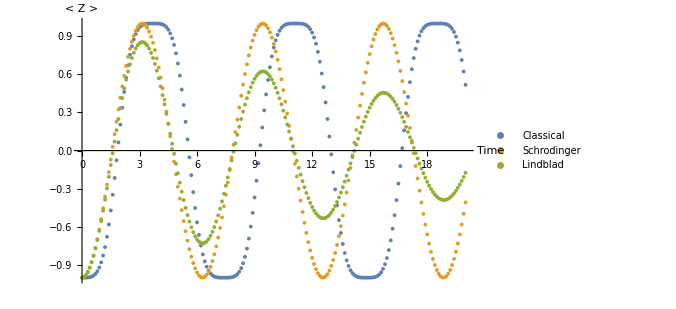

```mathematica
ListPlot[{cExpZ,schroRhoZ, lindRhoZ}, PlotLegends->Placed[{"Classical", "Schrodinger", "Lindblad"}, {0.75,0.8}], ImageSize->500, AxesLabel->{"Time", "< Z >"}]
```